## eBeam Correlation Plots

```mathematica
run="174";
```

```mathematica
ToString[run]
```

174

### Quadrant Plots

```mathematica
quadrant1=Flatten[Import["/Users/Max/ownCloud/Doktor/amoi0214_data/mustacheplot/run0"<>ToString[run]<>"_BinnedSpectraQuadrant_1"]];
quadrant2=Flatten[Import["/Users/Max/ownCloud/Doktor/amoi0214_data/mustacheplot/run0"<>ToString[run]<>"_BinnedSpectraQuadrant_2"]];
quadrant3=Flatten[Import["/Users/Max/ownCloud/Doktor/amoi0214_data/mustacheplot/run0"<>ToString[run]<>"_BinnedSpectraQuadrant_3"]];
quadrant4=Flatten[Import["/Users/Max/ownCloud/Doktor/amoi0214_data/mustacheplot/run0"<>ToString[run]<>"_BinnedSpectraQuadrant_4"]];
quadrant5=Flatten[Import["/Users/Max/ownCloud/Doktor/amoi0214_data/mustacheplot/run0"<>ToString[run]<>"_BinnedSpectraQuadrant_5"]];
quadrant6=Flatten[Import["/Users/Max/ownCloud/Doktor/amoi0214_data/mustacheplot/run0"<>ToString[run]<>"_BinnedSpectraQuadrant_6"]];
quadrant7=Flatten[Import["/Users/Max/ownCloud/Doktor/amoi0214_data/mustacheplot/run0"<>ToString[run]<>"_BinnedSpectraQuadrant_7"]];
quadrant8=Flatten[Import["/Users/Max/ownCloud/Doktor/amoi0214_data/mustacheplot/run0"<>ToString[run]<>"_BinnedSpectraQuadrant_8"]];
quadrant9=Flatten[Import["/Users/Max/ownCloud/Doktor/amoi0214_data/mustacheplot/run0"<>ToString[run]<>"_BinnedSpectraQuadrant_9"]];
```

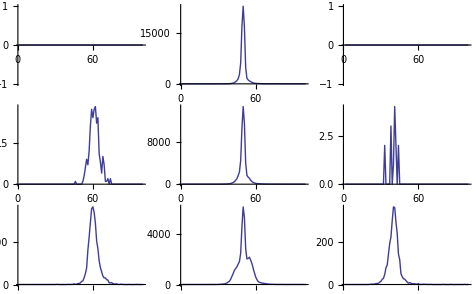

```mathematica
GraphicsGrid[{{ListLinePlot[quadrant3,PlotRange->All,PlotStyle->Thick],ListLinePlot[quadrant6,PlotRange->All,PlotStyle->Thick],ListLinePlot[quadrant9,PlotRange->All,PlotStyle->Thick]},{ListLinePlot[quadrant2,PlotRange->All,PlotStyle->Thick],ListLinePlot[quadrant5,PlotRange->All,PlotStyle->Thick],ListLinePlot[quadrant8,PlotRange->All,PlotStyle->Thick]},{ListLinePlot[quadrant1,PlotRange->All,PlotStyle->Thick],ListLinePlot[quadrant4,PlotRange->All,PlotStyle->Thick],ListLinePlot[quadrant7,PlotRange->All,PlotStyle->Thick]}}]
```

### Mustache Plot

#### Scatter Plot

```mathematica
xval=Flatten[Import["/Users/Max/ownCloud/Doktor/amoi0214_data/mustacheplot/run0"<>ToString[run]<>"_MustachePlot_xVals","Table"]];
yval=Flatten[Import["/Users/Max/ownCloud/Doktor/amoi0214_data/mustacheplot/run0"<>ToString[run]<>"_MustachePlot_yVals","Table"]];
Length[xval]==Length[yval]
```

True

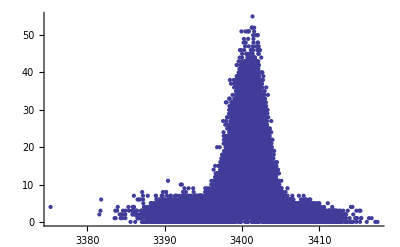

```mathematica
ListPlot[Table[{xval[[i]],yval[[i]]},{i,1,Length[xval]}]]
```

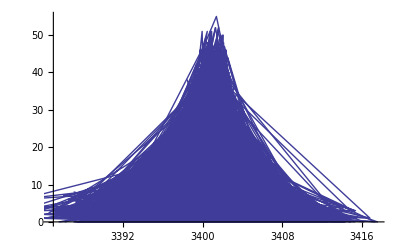

```mathematica
ListLinePlot[Table[{xval[[i]],yval[[i]]},{i,1,Length[xval]}]]
```

#### Average Plot

```mathematica
avgMustachePlot=Import["/Users/Max/ownCloud/Doktor/amoi0214_data/mustacheplot/run0"<>ToString[run]<>"_MustachePlot"];

Length[avgMustachePlot]
Total[avgMustachePlot]
```

30

{0.,0.,0.,1.,2.,0.,0.,0.,2.,3.,3.,3.,3.,3.,8.,11.,11.,17.,20.,16.,27.,37.,48.,72.,95.,81.,109.,155.,185.,201.,243.,293.,361.,404.,461.,545.,556.,688.,821.,769.,893.,1049.,986.,1174.,1218.,1295.,1254.,1142.,973.,899.,777.,755.,676.,707.,774.,891.,936.,1020.,1004.,914.,850.,784.,683.,608.,535.,461.,401.,344.,256.,265.,206.,159.,119.,95.,74.,66.,54.,47.,22.,21.,20.,17.,9.,10.,3.,6.,3.,4.,4.,0.,1.,2.,0.,2.,0.,0.,0.,0.,0.,0.}

```mathematica
ListPointPlot3D[avgMustachePlot,PlotRange->All]
```

-Graphics3D-